{{s→InterpolatingFunction[…],i→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

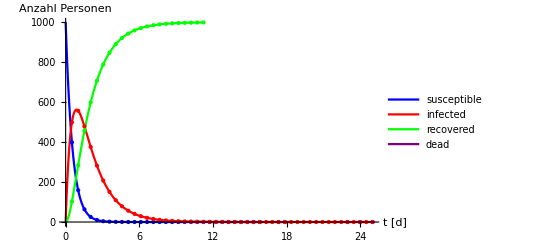

susceptile

{6.42889×10^-13}

infected

{0.000137264}

recovered

{1001.}

```mathematica
n=1000; (*Start Population*)
endt=25; (*Ende t der Simulation*)
b=1.8;(*Infektionsrate*)
k=0.65;(*Genesungsrate*)


system={
differenzialS=s'[t]==-b*s[t],(*Susceptile*)
differenzialI=i'[t]==b*s[t]-k*i[t],(*Infective*)
differenzialR=r'[t]==k*i[t](*Recovered*)

};
anfangswerte={
s[0]==n,
i[0]==1,
r[0]==0
};
lösung=NDSolve[{system,anfangswerte},{s,i,r},{t,0,100}](*löse das GLS*)
lösungS=First[s/.lösung];(*erhalte erstes Element von Liste*)
lösungI=First[i/.lösung];
lösungR=First[r/.lösung];


graph=
Plot[{lösungS[t],lösungI[t],lösungR[t]},{t,0,endt},
PlotRange->{0,n},
PlotStyle->{Blue,Red,Green,Purple},
PlotLegends->{"susceptible","infected","recovered"},
Mesh->Full,
AxesLabel->{"t [d]","Anzahl Personen"}
]
"susceptile"
s[endt]/.lösung
"infected"
i[endt]/.lösung
"recovered"
r[endt]/.lösung
```

```mathematica
{{□}, {□}}
```

{{□},{□}}